```mathematica
Quantum Harmonic Oscillator
```

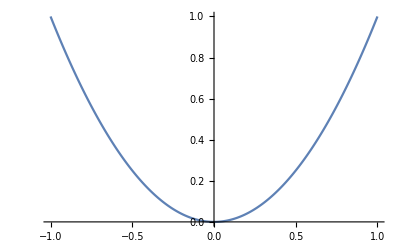

```mathematica
min=-1;max=1;step=500;
d=(max-min)/step;
V=Table[x^2,{x,Range[min,max,d]}];
ListLinePlot[V,PlotRange->All,DataRange->{min,max}]
```

```mathematica
En=0.07;
f=2(V-En);
```

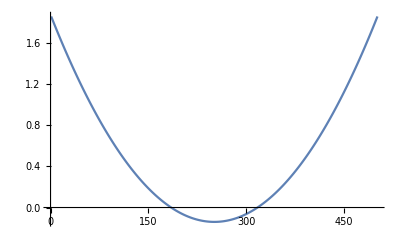

```mathematica
ListLinePlot[f]
```

```mathematica
u=ConstantArray[0,step];
g=ConstantArray[0,step];
u[[2]]=1;(*boundary conditions*)
g[[2]]=u[[2]](1-(d^2 f[[2]])/12);
```

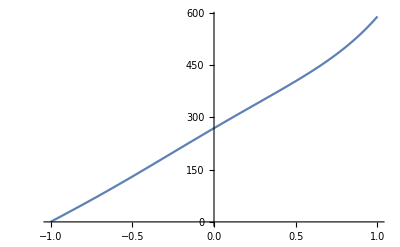

```mathematica
Do[g[[i+1]]=2 g[[i]]-g[[i-1]]+d^2 f [[i]]u[[i]];u[[i+1]]=g[[i+1]]/(1-(d^2 f[[i+1]])/12),{i,2,step-1,1}]
(*Do[g[[i-1]]=2 g[[i]]-g[[i+1]]+d^2 f [[i]]u[[i]];u[[i+1]]=g[[i-1]]/(1-(d^2 f[[i-1]])/12),{i,step/2+1,1,-1}]*)
ListLinePlot[g,PlotRange->All,DataRange->{min,max}]
```